```mathematica
ω=.
i=.
x=.
n=.
h=.
```

```mathematica
(* EQ 15 *)
gxib=Exp[∑_(i=1)^n β[[i]] x[[i]]];//Quiet
```

```mathematica
(* EQ 19 *)
pixiG=(1-(1-h)^(gxib)) ∏_(k=1)^(i-1) ((1-h)^(gxib));
```

```mathematica
(* EQ 32 *)
lnL=-ω ∑_(i=1)^n ((1-(1-h)^(Exp[x1[[i]] β1])) ∏_(k=1)^(i-1) ((1-h)^(Exp[x1[[k]]β1])))+Log[ω]∑_(i=1)^n (y[[i]] ) + ∑_(i=1)^n (y[[i]] Log[(1-(1-h)^(Exp[x1[[i]] β1])) ∏_(k=1)^(i-1) ((1-h)^(Exp[x1[[k]]β1]))])-∑_(i=1)^n Log[y[[i]]!];//Quiet
```

```mathematica
(* Hazard Functions *)
GM=b;
NB2=(i b^2)/(1+b (i-1));
DW2=1-b^(i^2-(i-1)^2);
DW3=1-Exp[-c i^b];
S=p (1-pi^i);
TL=(1-Exp[-1/d])/(1+Exp[-(i-c)/d]);
IFRSB=1-c/i;
IFRGSB=1-c/((i-1) α+1);
```

```mathematica
(* Covariate data *)
Cov1={0.0531,0.0619,0.158,0.081,1.046,1.75,2.96,4.97,0.42,4.7,0.9,1.5,2,1.2,1.2,2.2,7.6};
```

```mathematica
(* Loop to generate failure counts *)
ω=75;
FC=List[];
For[j=1,j≤17,j++,
i=j;
x={Cov1[[j]]};
FC=Append[FC,Part[RandomVariate[PoissonDistribution[ω pixiG/.{n->1,β->{0.12707767},h->NB2/.{b->0.08478873}}],1],1]];//Quiet
]
ω=.
FC
n=Length[FC]
```

{0,0,2,3,0,1,1,5,4,1,1,1,1,1,1,3,0}

17

```mathematica
(* Cummulative Failure Count *)
CummulativeFC = List[FC[[1]]];
For[j=2,j≤17,j++,
CummulativeFC=Append[CummulativeFC,FC[[j]]+CummulativeFC[[j-1]]];
]
CummulativeFC
```

{0,0,2,5,5,6,7,12,16,17,18,19,20,21,22,25,25}

```mathematica
(* MLEs *)
h=NB2;
lnLa=lnL/.{y-> FC,x1->Cov1};//Quiet
Rules=FindRoot[{{0==D[lnLa,ω]},{0==D[lnLa,β1]},{0==D[lnLa,b]}},{{ω,75},{β1,0.12707767},{b,0.08478873}},MaxIterations->100000]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100000 iterations.

{ω→8385.95,β1→0.0162141,b→0.00324432}

```mathematica
(* Model fit *)
j=.
Hω=∑_(i=1)^j ω(1-((1-h)^(Exp[x1[[i]] β1]))) ∏_(g=1)^(i-1) (1-h)^(Exp[x1[[g]]β1])/.Rules/.{x1->Cov1};//Quiet
HωList={};
For[k=1,k≤ n,
AppendTo[HωList,Hω/.j->k];
k=k+1;
];
HωList//N
```

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression g cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{1.42772,2.8554,4.28507,5.71271,7.16261,8.6289,10.124,11.6683,13.1025,14.6396,16.0845,17.5433,19.0137,20.465,21.9159,23.3904,24.9994}

```mathematica
(* Goodness of fit *)
AIC=2 p-2 lnLa/.Rules/.p-> 3
BIC=+ p Log[n]-2 lnLa/.Rules/.p-> 3
SSE=∑_(i=1)^n (HωList[[i]]-CummulativeFC[[i]])^2
```

61.1755

63.6751

60.9932

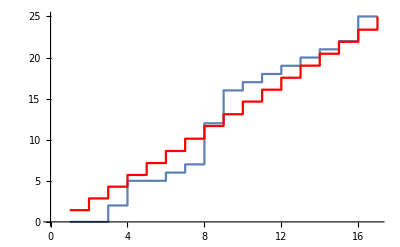

```mathematica
(* Plot data and model fit *)
gEmpirical=ListPlot[CummulativeFC,InterpolationOrder->0,Joined->True];
gFitted=ListPlot[HωList,PlotStyle->Red,Joined->True,InterpolationOrder->0];
Show[gEmpirical,gFitted]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Intervals=Table[i,{i,1,17}];(* NB2 doesn't give consistently good fits, forgo fitness test before export*)
Export["NB2_1cov_sim.xlsx",Transpose[{Intervals,FC,Cov1}]]
```

NB2_1cov_sim.xlsx